R51_1st

### Codes

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\dodo\Desktop\soothair_2nd\2_Systems_FullRev\R51_1st\PES

```mathematica
(*Species Specification*)numReac=1;
numProd=1;
numIntM=2;
numTraS=3;
(*Species Eenergy with zero-point correction*)
EReac={-846.694232443+-77.3304797767};(*R1+R2*)
EProd={-924.075455219};(*P1*)
EIntM={-924.012179047,-924.012962746};(*IM1,IM2*)
ETraS={-924.008102186,-923.968792952,-923.990676817};(*TS2,TS3,TS1*)
E0=EReac⟦1⟧;
EReac=(EReac-E0)*627.51;
EProd=(EProd-E0)*627.51;
EIntM=(EIntM-E0)*627.51;
ETraS=(ETraS-E0)*627.51;
(*Coordinates Settings*)
Emin=Min[EProd]-20;
Emax=Max[ETraS]+20;
xscaling=5;
xmax=xscaling*numTraS +1;
xmin=-1;
xlength=0.5;
(*PlotStyle Specificatoiin*)
FMT={13,Italic};
LineFMT= Thick; (*Dashed,Thick,CapForm[Round],JoinForm[Round]*)
plotframe={{Style["Energy  (kcal/mol)",16],},{Style["Internal Reaction Coordinates",16],}};
arrowsize=Small;
imageposition=25;
imagesize=3;
(*Check*)
Print[EReac];
Print[EProd];
Print[EIntM];
Print[ETraS];
If [Dimensions[EReac]⟦1⟧== numReac,Print["Number of Reactants, Right"],Print["Number of Reactants, Wrong"]];
If [Dimensions[EProd]⟦1⟧== numProd,Print["Number of Products, Right"],Print["Number of Products, Wrong"]];
If [Dimensions[EIntM]⟦1⟧== numIntM,Print["Number of InterMediates, Right"],Print["Number of InterMediates, Wrong"]];
If [Dimensions[ETraS]⟦1⟧== numTraS,Print["Number of TransitionStates, Right"],Print["Number of TransitionStates, Wrong"]];
(*IM1={{energy},{name},{position},{offset},{picpath},{piclayer}}*)
(*TS1={{energy},{name},{position},{offset},{picpath},{piclayer},{one end,the other end}}*)
Reac[i_]:={{EReac⟦i⟧},{"R"<>ToString[i]},{0,EReac⟦i⟧},{0,-1},{NotebookDirectory[]<>"R"<>ToString[i]<>".tif"},{0,imageposition}};
Prod[i_]:={{EProd⟦i⟧},{"P"<>ToString[i]},{xmax-1,EProd⟦i⟧},{0,-1},{NotebookDirectory[]<>"P"<>ToString[i]<>".tif"},{0,imageposition}};
IntM[i_]:={{EIntM⟦i⟧},{"IM"<>ToString[i]},{i*xscaling,EIntM⟦i⟧},{0,-1},{NotebookDirectory[]<>"IM"<>ToString[i]<>".tif"},{0,imageposition}};
TraS[i_]:={{ETraS⟦i⟧},{"TS"<>ToString[i]},{(i-0.5)*xscaling,ETraS⟦i⟧},{0,-1},{NotebookDirectory[]<>"TS"<>ToString[i]<>".tif"},{0,imageposition}};
(*Specific Settings of Reac Prod IntM and TranS*)
```

{0.}

{-31.8417}

{7.86469,7.37291}

{10.423,35.0899,21.3576}

Number of Reactants, Right

Number of Products, Right

Number of InterMediates, Right

Number of TransitionStates, Right

```mathematica
(*Default position is TraS[i]⟦3⟧ which is linking the two nearby stable state, if the following is not specified*)
TraS[3]=Append[TraS[3],{Reac[1][[3]],IntM[1][[3]]}];
TraS[1]=Append[TraS[1],{IntM[1][[3]],IntM[2][[3]]}];
TraS[2]=Append[TraS[2],{IntM[2][[3]],Prod[1][[3]]}];
(*TraS[1]⟦7⟧={Reac[2]⟦3⟧,IntM[1]⟦3⟧};
TraS[2]⟦7⟧={IntM[1]⟦3⟧,IntM[2]⟦3⟧};
TraS[3]⟦7⟧={IntM[2]⟦3⟧,IntM[3]⟦3⟧};
TraS[4]⟦7⟧={IntM[3]⟦3⟧,Prod[1]⟦3⟧};*)
```

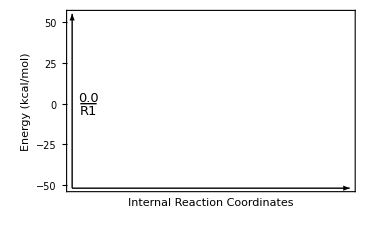

```mathematica
ReacPlot[i_]:=Graphics[
{   
{Thick,LineFMT,Line[{{Reac[i]⟦3,1⟧-xlength,Reac[i]⟦3,2⟧},{Reac[i]⟦3,1⟧+xlength,Reac[i]⟦3,2⟧}}]},Text[Style[Reac[i]⟦2,1⟧,FMT],Reac[i]⟦3⟧,Reac[i]⟦4⟧ *(-1)],
Text[Style[NumberForm[Reac[i]⟦1,1⟧,{3,1}],FMT],Reac[i]⟦3⟧,Reac[i]⟦4⟧ ],
Arrowheads[arrowsize],Arrow[{{xmin,Emin},{xmax,Emin}}],Arrow[{{xmin,Emin},{xmin,Emax}}](*,
Inset[Import[Reac[i]⟦5,1⟧],Reac[i]⟦3⟧-Reac[i]⟦6⟧,Automatic,imagesize]*)
},
PlotRange->{{xmin,xmax},{Emin,Emax}},AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,FrameTicks-> {None,Automatic}];
Reacimage=Show[Table[ReacPlot[s],{s,numReac}]]
```

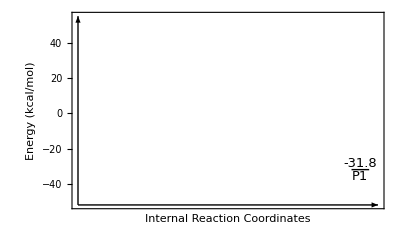

```mathematica
ProdPlot[i_]:=Graphics[
{   
{Thick,LineFMT,Line[{{Prod[i]⟦3,1⟧-xlength,Prod[i]⟦3,2⟧},{Prod[i]⟦3,1⟧+xlength,Prod[i]⟦3,2⟧}}]},Text[Style[Prod[i]⟦2,1⟧,FMT],Prod[i]⟦3⟧,Prod[i]⟦4⟧ *(-1)],
Text[Style[NumberForm[Prod[i]⟦1,1⟧,{3,1}],FMT],Prod[i]⟦3⟧,Prod[i]⟦4⟧ ],
Arrowheads[arrowsize],Arrow[{{xmin,Emin},{xmax,Emin}}],Arrow[{{xmin,Emin},{xmin,Emax}}](*,
Inset[Import[Prod[i]⟦5,1⟧],Prod[i]⟦3⟧-Prod[i]⟦6⟧,Automatic,imagesize]*)
},
PlotRange->{{xmin,xmax},{Emin,Emax}},AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,FrameTicks-> {None,Automatic}];
Prodimage=Show[Table[ProdPlot[s],{s,numProd}]]
```

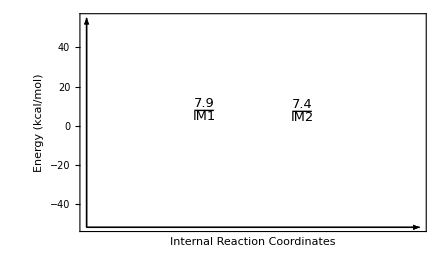

```mathematica
IntMPlot[i_]:=Graphics[
{   
{Thick,LineFMT,Line[{{IntM[i]⟦3,1⟧-xlength,IntM[i]⟦3,2⟧},{IntM[i]⟦3,1⟧+xlength,IntM[i]⟦3,2⟧}}]},Text[Style[IntM[i]⟦2,1⟧,FMT],IntM[i]⟦3⟧,IntM[i]⟦4⟧ *(-1)],
Text[Style[NumberForm[IntM[i]⟦1,1⟧,{3,1}],FMT],IntM[i]⟦3⟧,IntM[i]⟦4⟧ ],
Arrowheads[arrowsize],Arrow[{{xmin,Emin},{xmax,Emin}}],Arrow[{{xmin,Emin},{xmin,Emax}}](*,
Inset[Import[IntM[i]⟦5,1⟧],IntM[i]⟦3⟧-IntM[i]⟦6⟧,Automatic,imagesize]*)
},
PlotRange->{{xmin,xmax},{Emin,Emax}},AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,FrameTicks-> {None,Automatic}];
IntMimage=Show[Table[IntMPlot[s],{s,numIntM}]]
```

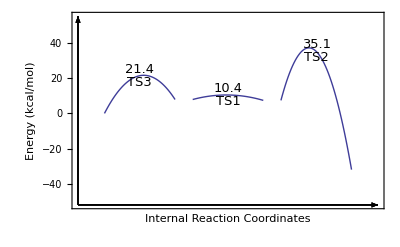

```mathematica
TraSPlot[i_]:=Graphics[
{   (*BSplineCurve[{TraS[i]⟦7,1⟧+{xlength,0},{TraS[i]⟦7,1,1⟧/2+TraS[i]⟦7,2,1⟧/2,TraS[i]⟦3,2⟧},TraS[i]⟦7,2⟧-{xlength,0}},SplineDegree-> 1],*)
Text[Style[TraS[i]⟦2,1⟧,FMT],{TraS[i]⟦7,1,1⟧/2+TraS[i]⟦7,2,1⟧/2,TraS[i]⟦3,2⟧},TraS[i]⟦4⟧ *(-1)],
Text[Style[NumberForm[TraS[i]⟦1,1⟧,{3,1}],FMT],{TraS[i]⟦7,1,1⟧/2+TraS[i]⟦7,2,1⟧/2,TraS[i]⟦3,2⟧},TraS[i]⟦4⟧ ],
Arrowheads[arrowsize],Arrow[{{xmin,Emin},{xmax,Emin}}],Arrow[{{xmin,Emin},{xmin,Emax}}]
},
PlotRange->{{xmin,xmax},{Emin,Emax}},AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,FrameTicks-> {None,Automatic}];
Curve[i_]:=Interpolation[{TraS[i]⟦7,1⟧+{xlength,0},{TraS[i]⟦7,1,1⟧/2+TraS[i]⟦7,2,1⟧/2,TraS[i]⟦3,2⟧},TraS[i]⟦7,2⟧-{xlength,0}}, InterpolationOrder->2];
TraSCurvePlot[i_]:=Plot[Curve[i][x],{x,TraS[i]⟦7,1,1⟧+xlength,TraS[i]⟦7,2,1⟧-xlength}
,AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,Ticks-> {None,Automatic}];
TraSimage=Show[Table[{TraSCurvePlot[s],TraSPlot[s]},{s,numTraS}],PlotRange->{{xmin,xmax},{Emin,Emax}},AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,FrameTicks-> {None,Automatic}]
(*Show[Table[TraSPlot[s],{s,numTraS}]]*)
```

```mathematica
Show[Reacimage,Prodimage,IntMimage,TraSimage]
```